```mathematica
Πpar[θ_,u_,mD_]:=mD^2/2((2-2 u^2-u^4 Cos[θ]^2 Sin[θ]^2)/((1-u^2 Sin[θ]^2)^2)-((2+u^2 Sin[θ]^2)(1-u^2)u Cos[θ])/(2(1-u^2 Sin[θ]^2)^(5/2))Log[(u Cos[θ]+√(1-u^2 Sin[θ]^2))/(u Cos[θ]-√(1-u^2 Sin[θ]^2))]);
```

```mathematica
ReVcold[r_,mD_,u_,α_]:=-α/r+α NIntegrate[Sin[θ] √Re[Πpar[θ,u,mD]] Exp[-√Re[Πpar[θ,u,mD]]r Cos[θ]],{θ,0,π/2}];
```

```mathematica
ϵRe[r_,mD_,u_]:=1/(4π)(2/r NIntegrate[Cos[θ]Sin[θ]Re[Πpar[θ,u,mD]]Exp[-√Re[Πpar[θ,u,mD]]r Cos[θ]],{θ,0,π/2}]- NIntegrate[Cos[θ]^2 Sin[θ] Re[Πpar[θ,u,mD]]^(3/2)Exp[-√Re[Πpar[θ,u,mD]]r Cos[θ]],{θ,0,π/2}]);
```

```mathematica
ϵold[r_,mD_,T_]:=-(ⅇ^(-mD r) mD^2)/(4π r)-ⅈ T(mD √π MeijerG[{{-1/2},{}},{{1/2,1/2},{0}},(mD^2 r^2)/4])/(4 π r);
```

```mathematica
ImVcold[r_,mD_,u_,α_,T_]:=-2 α T NIntegrate[Sin[x]((2+u^2 Sin[x]^2)(1-u^2)^(3/2))/(2(1-u^2 Sin[x]^2)^(5/2))mD^2/(Πpar[x,u,mD]-Conjugate[Πpar[x,u,mD]])(Sinh[√Πpar[x,u,mD] r Cos[x]]SinhIntegral[√Πpar[x,u,mD] r Cos[x]]-Cosh[√Πpar[x,u,mD] r Cos[x]]CoshIntegral[√Πpar[x,u,mD] r Cos[x]]-Sinh[√Conjugate[Πpar[x,u,mD]] r Cos[x]]SinhIntegral[√Conjugate[Πpar[x,u,mD]] r Cos[x]]+Cosh[√Conjugate[Πpar[x,u,mD]] r Cos[x]]CoshIntegral[√Conjugate[Πpar[x,u,mD]] r Cos[x]]),{x,0,π/2}];
```

```mathematica
ϵIm[r_,mD_,u_,T_]:=Re[2/(4π)T NIntegrate[Sin[x]((2+u^2 Sin[x]^2)(1-u^2)^(3/2))/(2(1-u^2 Sin[x]^2)^(5/2))mD^2/(Πpar[x,u,mD]-Conjugate[Πpar[x,u,mD]])1/r Cos[x] (2 √Conjugate[Πpar[x,u,mD]] (CoshIntegral[r √Conjugate[Πpar[x,u,mD]] Cos[x]] Sinh[r √Conjugate[Πpar[x,u,mD]] Cos[x]]-Cosh[r √Conjugate[Πpar[x,u,mD]] Cos[x]] SinhIntegral[r √Conjugate[Πpar[x,u,mD]] Cos[x]])+r Conjugate[Πpar[x,u,mD]] Cos[x] (Cosh[r √Conjugate[Πpar[x,u,mD]] Cos[x]] CoshIntegral[r √Conjugate[Πpar[x,u,mD]] Cos[x]]-Sinh[r √Conjugate[Πpar[x,u,mD]] Cos[x]] SinhIntegral[r √Conjugate[Πpar[x,u,mD]] Cos[x]])+√Πpar[x,u,mD] (-CoshIntegral[r Cos[x] √Πpar[x,u,mD]] (r Cos[x] Cosh[r Cos[x] √Πpar[x,u,mD]] √Πpar[x,u,mD]+2 Sinh[r Cos[x] √Πpar[x,u,mD]])+(2 Cosh[r Cos[x] √Πpar[x,u,mD]]+r Cos[x] √Πpar[x,u,mD] Sinh[r Cos[x] √Πpar[x,u,mD]]) SinhIntegral[r Cos[x] √Πpar[x,u,mD]])),{x,0,π/2}]];
```

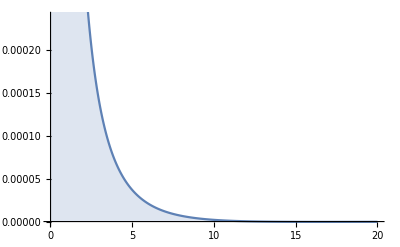

```mathematica
DiscretePlot[ϵIm[r,0.2,0.2,0.155],{r,1/100,20,1/100}]
```

```mathematica
ϵIm[2,2/10,2/10,155/1000]/0.00096938357820498633466304779014327034
```

0.33149

```mathematica
ϵIm[5,2/10,2/10,155/1000]/0.00031113478331159373990654740654444683
```

0.118574

```mathematica
D[(Sinh[√f[x,u,mD] r Cos[x]]SinhIntegral[√f[x,u,mD] r Cos[x]]-Cosh[√f[x,u,mD] r Cos[x]]CoshIntegral[√f[x,u,mD] r Cos[x]]-Sinh[√Conjugate[f[x,u,mD]] r Cos[x]]SinhIntegral[√Conjugate[f[x,u,mD]] r Cos[x]]+Cosh[√Conjugate[f[x,u,mD]] r Cos[x]]CoshIntegral[√Conjugate[f[x,u,mD]] r Cos[x]]),{r,2}]+2/r D[(Sinh[√f[x,u,mD] r Cos[x]]SinhIntegral[√f[x,u,mD] r Cos[x]]-Cosh[√f[x,u,mD] r Cos[x]]CoshIntegral[√f[x,u,mD] r Cos[x]]-Sinh[√Conjugate[f[x,u,mD]] r Cos[x]]SinhIntegral[√Conjugate[f[x,u,mD]] r Cos[x]]+Cosh[√Conjugate[f[x,u,mD]] r Cos[x]]CoshIntegral[√Conjugate[f[x,u,mD]] r Cos[x]]),r]//FullSimplify
```

1/r Cos[x] (2 √Conjugate[f[x,u,mD]] (CoshIntegral[r √Conjugate[f[x,u,mD]] Cos[x]] Sinh[r √Conjugate[f[x,u,mD]] Cos[x]]-Cosh[r √Conjugate[f[x,u,mD]] Cos[x]] SinhIntegral[r √Conjugate[f[x,u,mD]] Cos[x]])+r Conjugate[f[x,u,mD]] Cos[x] (Cosh[r √Conjugate[f[x,u,mD]] Cos[x]] CoshIntegral[r √Conjugate[f[x,u,mD]] Cos[x]]-Sinh[r √Conjugate[f[x,u,mD]] Cos[x]] SinhIntegral[r √Conjugate[f[x,u,mD]] Cos[x]])+√f[x,u,mD] (-CoshIntegral[r Cos[x] √f[x,u,mD]] (r Cos[x] Cosh[r Cos[x] √f[x,u,mD]] √f[x,u,mD]+2 Sinh[r Cos[x] √f[x,u,mD]])+(2 Cosh[r Cos[x] √f[x,u,mD]]+r Cos[x] √f[x,u,mD] Sinh[r Cos[x] √f[x,u,mD]]) SinhIntegral[r Cos[x] √f[x,u,mD]]))